## Quantum States and Amplitudes

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Quantum Amplitudes

State Vector

Density Matrix

### State Vectors and Amplitudes

You have already seen bra-ket notation for quantum states like 0 or 1. What about other kinds of quantum states? For example, the result of applying a Hadamard gate to the register state:

```mathematica
state1=QuantumOperator["H"]@QuantumState["0"]
```

QuantumState[…]

```mathematica
state1["BlochPlot"]
```

-Graphics3D-

You can see from the Bloch plot that this state is plainly neither 0 nor 1.

```mathematica
state1["Formula"]
```

1/(√2)0+1/(√2)1

This state is instead a particular combination of 0 and 1. Since it is a linear combination, this suggests that quantum states can be represented by vectors and operators can be represented by matrices.

```mathematica
state1["StateVector"]//MatrixForm//TraditionalForm
```

(1/(√2)
1/(√2))

```mathematica
QuantumOperator["H"]["Matrix"]//MatrixForm//TraditionalForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

Notice the relationship between the vector coefficients and the probabilities for each classical outcome.

```mathematica
state1["Probabilities"]
```

<|0→1/2,1→1/2|>

The computational basis is called a basis because the states 0 and 1 can be used as basis elements for the complex vector space ℂ^2:

```mathematica
QuantumState["0"]["StateVector"]//MatrixForm//TraditionalForm
```

(1
0)

```mathematica
QuantumState["1"]["StateVector"]//MatrixForm//TraditionalForm
```

(0
1)

The coefficients of each basis element are known as the quantum amplitudes. A quantum state can be defined by giving its amplitudes:

```mathematica
state2=QuantumState[{a,b}]
```

QuantumState[…]

This can be written in Dirac notation:

```mathematica
state2["Formula"]//TraditionalForm
```

a0+b1

The norm squared of the normalized amplitudes give the probability for measuring each of the basis elements as the outcome of a measurement interaction:

```mathematica
state2["Probabilities"]
```

<|0→Abs[a]^2/(Abs[a]^2+Abs[b]^2),1→Abs[b]^2/(Abs[a]^2+Abs[b]^2)|>

Typically, qubit amplitudes are already normalized such that (|a|)^2+(|b|)^2=1.

```mathematica
state2["Probabilities"]//Map[#/.Abs[a]^2+Abs[b]^2->1&]
```

<|0→Abs[a]^2,1→Abs[b]^2|>

This quantum state can also be represented as a state vector:

```mathematica
state2["StateVector"]//MatrixForm//TraditionalForm
```

(a
b)

Some quantum states require a matrix representation known as the density matrix:

```mathematica
state2["DensityMatrix"]//MatrixForm//TraditionalForm
```

(a Conjugate[a] | a Conjugate[b]
b Conjugate[a] | b Conjugate[b])

Keep in mind that the amplitudes can be complex numbers. The following plot lets you explore the relationship between the probability of measuring each state in the computational basis and the complex phase difference between each amplitude:

```mathematica
Manipulate[
QuantumState[{Sqrt[P],Sqrt[1-P]Exp[I Θ]}]["BlochPlot",PlotLabel->QuantumState[{Sqrt[p],Sqrt[1-p]Exp[I θ]}]["Formula"]],
{{P,.5,TraditionalForm["P(0)"]},0,1},{{Θ,0,"Relative Phase"},0,2Pi},TrackedSymbols:>{P,Θ},ControlPlacement->Top,Initialization:>Needs["Wolfram`QuantumFramework`"]
]
```

#### Example

Consider the quantum state 1/2 0+(√3)/2 1.

What is the state vector, the density matrix, the Bloch plot, and the measurement distribution in the computational basis?

##### Solution

Define the state with the given amplitudes:

```mathematica
state3=QuantumState[{1/2,√3/2}]
```

QuantumState[…]

Probabilities are the (normalized) norm squared of these amplitudes:

```mathematica
state3["Probabilities"]
```

<|0→1/4,1→3/4|>

Compute the state vector, density matrix, and Bloch plot:

```mathematica
state3["StateVector"]//MatrixForm//TraditionalForm
```

(1/2
(√3)/2)

```mathematica
state3["DensityMatrix"]//MatrixForm//TraditionalForm
```

(1/4 | (√3)/4
(√3)/4 | 3/4)

```mathematica
state3["BlochPlot"]
```

-Graphics3D-

The Bloch vector can be given in either spherical or Cartesian coordinates:

```mathematica
state3["BlochSphericalCoordinates"]
```

{1,(2 π)/3,0}

```mathematica
state3["BlochCartesianCoordinates"]
```

{(√3)/2,0,-1/2}

### States vs Measurements

While a measurement operation is always necessary to obtain practical results from quantum circuits, it is often helpful to analyze what happens to quantum states as each gate operation is applied to the qubits.

Consider the following quantum circuit:

```mathematica
circuit1=QuantumCircuitOperator[{QuantumState[{1/2,√3/2},"Label"->Subscript[ψ,0]],"X","H","X"}]
```

QuantumCircuitOperator[…]

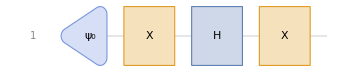

```mathematica
circuit1["Diagram"]
```

What happens to the initial state after each gate is applied?

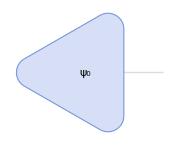
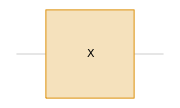
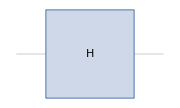
State 0 | State 1 | State 2 | State 3
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{states=ComposeList[circuit1["Operators"][[2;;]],circuit1["Operators"][[1]]["State"]]},
Grid[{Table[Style["State "<>ToString[n-1],"Text"],{n,Length[states]}],Map[#["BlochPlot",PlotLabel->Highlighted[#["FullSimplify"]["Formula"],Background->LightOrange]]&,states],Map[#["CircuitDiagram",ImageSize->Small,"WireLabels"->None]&,circuit1["Operators"]]},Alignment->Center,Frame->All,Spacings->{1,2}]
]
```

You can use the "AmplitudesPlot" property as another way of visualizing quantum states:

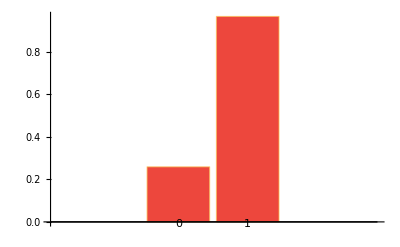

```mathematica
circuit1[]["FullSimplify"]["AmplitudesPlot",ChartLegends->Automatic]
```

Recall that amplitudes do not have to be real numbers. They can take on complex values. What about a similar circuit but different initial state?

```mathematica
circuit2=QuantumCircuitOperator[{QuantumState[{1/2,ⅈ√3/2}],"X","H","X"}]
```

QuantumCircuitOperator[…]

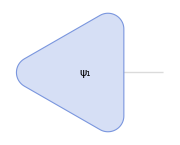
State 0 | State 1 | State 2 | State 3
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{circuit=circuit2,states},
states=ComposeList[circuit["Operators"][[2;;]],circuit["Operators"][[1]]["State"]];
Grid[{Table[Style["State "<>ToString[n-1],"Text"],{n,Length[states]}],Map[#["BlochPlot",PlotLabel->Highlighted[#["Simplify"]["Formula"],Background->LightOrange]]&,states],Map[#["CircuitDiagram",ImageSize->Small,"WireLabels"->None]&,circuit["Operators"]]},Alignment->Center,Frame->All,Spacings->{1,2}]
]
```

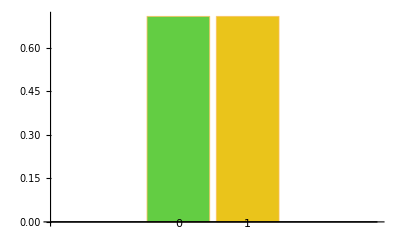

```mathematica
circuit2[]["Simplify"]["AmplitudesPlot",ChartLegends->Automatic]
```

Even though the measurement distributions for each of the two initial states were identical, they are different quantum states. Thus, this circuit has very different effects on them.

```mathematica
QuantumState[{1/2,√3/2}]["Probabilities"]
```

<|0→1/4,1→3/4|>

```mathematica
QuantumState[{1/2,ⅈ√3/2}]["Probabilities"]
```

<|0→1/4,1→3/4|>

```mathematica
circuit1[]==circuit2[]
```

False